# Lab1: Shadowing a Particle

## Background

Analyze the trajectory x(t) of a particle of mass m in a given force field f(x) and with given initial conditions x(t_0) and v(t_0). Study the dependency of the trajectory on disturbances in the initial conditions by simulating a system of particles with slightly different initial conditions. Study the dependency of the numerically computed trajectory on the time-step size h by comparing with a given reference trajectory representing the exact solution.

System of N_p particles in 2D of mass m is governed by Newton’s equations of motion. The force f(x) and potential energy E_p(x) for each particle is:

f(x)=m g-∑_(k=1)^5 f_k/r_k^2 exp(-(‖x-p_k‖)^2/(2 r_k^2)) (x-p_k)

E_p(x)=-m g·x-∑_(k=1)^5 f_k exp(-(‖x-p_k‖)^2/(2 r_k^2))

This force and potential represents gravity g and k = 1, 2, ..., 5 spherically symmetric attractive force fields with center position p_k, strength f_k and radius r_k, respectively.

#### General Parameters

N_p=500,	m = 1 kg,	L = 5 m

#### Initial Conditions

t_0=0 s,	t_f=3 s,	h=0.01 s,

x(t_0)=(-L,L),		v(t_0)=(5,10)m/s

#### Physical Constants

g=(0,-9.81)m/s^2

#### Symmetric Attractive Force Fields

f_1=32N,	f_2=40N,	f_3=28N,	f_4=16N,	f_5=20N

r_1=0.3L,	r_2=0.2L,	r_3=0.4L,	r_4=0.5L,	r_5=0.3L

p_1=(-0.2,0.8)L,
	p_2=(-0.3,-0.8)L,
	p_3=(-0.6,0.1)L,
	p_4=(0.4,0.7)L, 
	p_5=(0.8,-0.3)L

#### Position and Velocity Disturbances

δx=(δx,δy); | δx,δy∈(-0.02,0.02)L
δv=(δv_x,δv_y); | δv_x,δv_y∈(-0.02v(t_0),0.02v(t_0))

## Parameters

```mathematica
Remove["`*"]; (* Remove all global symbols *)
```

#### General Parameters

```mathematica
L:=5;  (* Characteristic length of the system *)
```

```mathematica
m:=1; (* Particle mass *)
```

#### Initial Conditions

```mathematica
t0=0; (* Initial time *)
```

```mathematica
tf=3; (* Final time *)
```

```mathematica
x0:={-L,-L}; (* Initial position *)
```

```mathematica
v0:={5,10}; (* Initial velocity *)
```

#### Physical Constants

```mathematica
g:={0,-9.81}; (* Acceleration of gravity *)
```

#### Symmetric Attractive Force Fields

```mathematica
f:={32,40,28,16,20}; (* Force strength *)
```

```mathematica
r:={0.3,0.2,0.4,0.5,0.3}L; (* Force radius *)
```

```mathematica
p:=({{-0.2, 0.8}, {-0.3, -0.8}, {-0.6, 0.1}, {0.4, 0.7}, {0.8, -0.3}})L;(* Center position of the force *)
```

## Forces and Energy

#### Total Force

```mathematica
F[x_?VectorQ]:= m g- ∑_(k=1)^5 (f_⟦k⟧/r_⟦k⟧^2 Exp[-Norm[x-p_⟦k⟧]^2/(2 r_⟦k⟧^2)](x-p_⟦k⟧));
```

#### Potential and Kinetic Energy

```mathematica
Ep[x_?VectorQ]:= -m g.x- ∑_(k=1)^5 (f_⟦k⟧Exp[-Norm[x-p_⟦k⟧]^2/(2 r_⟦k⟧^2)]);
```

```mathematica
Ek[v_?VectorQ]:=(m v.v)/2;
```

## Equations of Motion

```mathematica
SolveODE[
t0_,tf_,
x0_?VectorQ,v0_?VectorQ,
method_:Automatic,h_:Automatic
]:=Module[ 
{X,V, sol},
sol=NDSolve[
{
(* Differential Equations: *)
	X'[t]==V[t],
	m V'[t]==F[ X[t] ],
(* Initial conditions: *)
	X[t0]==x0,
	V[t0]==v0
},
{X,V}, (* Dependent variables *)
{t,t0,tf} (* Range of the independent variable *)
,Method->method
,StartingStepSize->h
,MaxStepSize->h
,MaxSteps->Infinity
];
( {X,V}/.sol )[[1]]
];
```

## Reference Solution, RK4, h = 1e-4

```mathematica
X$ref={-3.983781315868414,-5.118978158404967};
Etot$ref=13.008837864965010;
```

## Solution, Runge-Kutta, h = 0.01

```mathematica
{X,V}=SolveODE[t0,tf,x0,v0,"ExplicitRungeKutta",0.01];
```

```mathematica
NumberForm[Norm[X[tf]-X$ref],20]
```

3.377978811938265×10^-11

```mathematica
NumberForm[Abs[Ep[X[tf]]+Ek[V[tf]]-Etot$ref],20]
```

2.967155410260602×10^-10

## Solution, Forward Euler, h = 0.01

```mathematica
{X,V}=SolveODE[t0,tf,x0,v0,"ExplicitEuler",0.01];
```

```mathematica
NumberForm[Norm[X[tf]-X$ref],20]
```

0.2517073657616581

```mathematica
NumberForm[Abs[Ep[X[tf]]+Ek[V[tf]]-Etot$ref],20]
```

2.341932983396703

## Solution, Automatic

```mathematica
{X,V}=SolveODE[t0,tf,x0,v0];
```

```mathematica
NumberForm[Norm[X[tf]-X$ref],20]
```

5.85117449696673×10^-7

```mathematica
NumberForm[Abs[Ep[X[tf]]+Ek[V[tf]]-Etot$ref],20]
```

3.176574857377545×10^-6

## Plots

```mathematica
<<VectorFieldPlots`;
```

```mathematica
pathPlot:=ParametricPlot[
{X[t]_⟦1⟧,X[t]_⟦2⟧},
{t,t0,tf},
PlotStyle->{Thickness[0.005],Ticks->{1,1},Red}
];
```

```mathematica
forceFieldPlot:=VectorFieldPlot[
F[{x1,x2}], 
{x1, -1.2L, 1.2L}, {x2, -1.2L,1.2 L},
PlotPoints->20
];
```

```mathematica
potentialPlot:=ContourPlot[
Ep[{x1,x2}],
{x1,-1.2L,1.2L},{x2,-1.2L,1.2L}
];
```

```mathematica
pathPlot3D:=ParametricPlot3D[
{X[t]_⟦1⟧,X[t]_⟦2⟧,Ep[X[t]]},
{t,t0,tf},
PlotStyle->{Thickness[0.005],Red}
];
```

```mathematica
potentialPlot3D:=Plot3D[
Ep[{x1,x2}],
{x1,-1.2L,1.2L},{x2,-1.2L,1.2L}
];
```

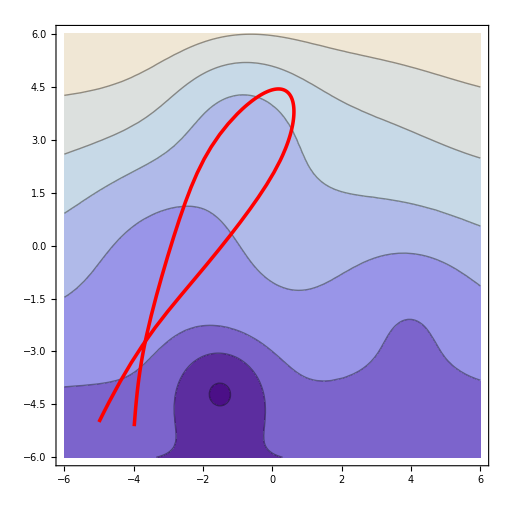

```mathematica
Show[ potentialPlot,pathPlot ]
```

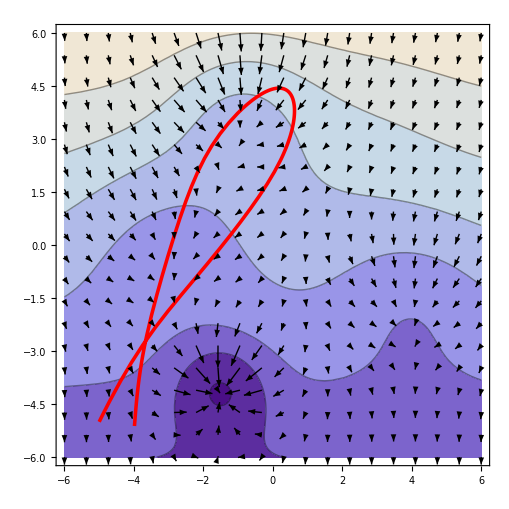

```mathematica
Show[ potentialPlot,forceFieldPlot,pathPlot ]
```

```mathematica
Show[ potentialPlot3D, pathPlot3D ]
```

-Graphics3D-

## Solution without Gravitation Field

```mathematica
g={0,0};
tf=100;
{X,V}=SolveODE[ t0,tf,{1,0},{0,1} ];
```

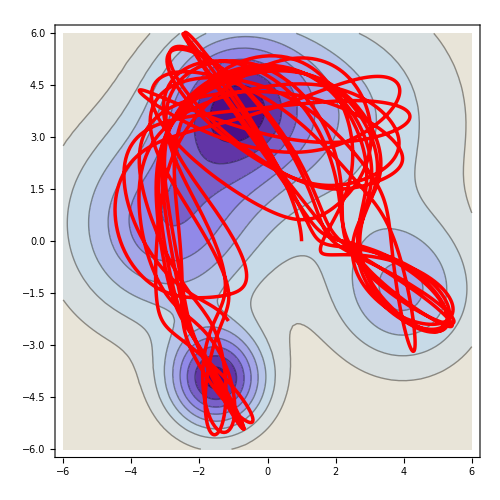

```mathematica
Show[ potentialPlot, pathPlot ]
```

```mathematica
Show[ potentialPlot3D, pathPlot3D ]
```

-Graphics3D-